```mathematica
Clear[a,b,fs,L];
(*using a generic L until I can figure out how to introduce it as a variable*)
(*trying to figure out how to define functions as peicewise in mathematica*)
(*f[x_]:=x*(1+Abs[x])/;-1≤x<1;
f[x_]:=f[x+2]/;x≥1OR x<-1; 
f[1],f[3]  *)
```

```mathematica
L=1;
fbas[x_]:=(1+x)/;-L≤x<L
f[x_]:=fbas[Mod[x,2×L,-L]]
```

```mathematica
N[f[3]]
```

0.

```mathematica
(*Defining the function as peicewise*)
```

```mathematica
(*g[x_]:=Piecewise[{{x*(1+Abs[x]),-1<=0<1},{f[x+2],x≥1}}];
g[3] *)
```

12

```mathematica
(*Defining the shifted function via Prof. Clark*)
```

```mathematica
(*defining the function to be approximated by the Fourier series*)
a[0]=Integrate[f(x),{x,-L,L}]
```

0

```mathematica
a[n_]=(∫_-L^L f(x)*Cos[(n*Pi*x)/L]ⅆx)/(2L)
```

0

```mathematica
b[n_]=FullSimplify[(∫_-L^L f(x)*Sin[(n*Pi*x)/L]ⅆx)/L]
```

(2 f (-n π Cos[n π]+Sin[n π]))/(n^2 π^2)

```mathematica
coeffs=Table[{a[i],b[i]},{i,1,10}];
TableForm[coeffs]
```

0 | (2 f)/π
0 | -f/π
0 | (2 f)/(3 π)
0 | -f/(2 π)
0 | (2 f)/(5 π)
0 | -f/(3 π)
0 | (2 f)/(7 π)
0 | -f/(4 π)
0 | (2 f)/(9 π)
0 | -f/(5 π)

```mathematica
coeffs[[1]]
```

{0,(2 f)/π}

```mathematica
coeffs[[2,1]]
```

0

```mathematica
fs[k_,x_]:=coeffs[[k,1]]*Cos[k*Pi*x/L]+coeffs[[k,2]]*Sin[k*Pi*x/L]
```

```mathematica
fourier[n_,x_]:=a[0]+∑_(k=1)^n fs[k,x]
```

```mathematica
fourier[5,x]
```

(2 f Sin[π x])/π-(f Sin[2 π x])/π+(2 f Sin[3 π x])/(3 π)-(f Sin[4 π x])/(2 π)+(2 f Sin[5 π x])/(5 π)

```mathematica
fourier[10,x]
```

(2 f Sin[π x])/π-(f Sin[2 π x])/π+(2 f Sin[3 π x])/(3 π)-(f Sin[4 π x])/(2 π)+(2 f Sin[5 π x])/(5 π)-(f Sin[6 π x])/(3 π)+(2 f Sin[7 π x])/(7 π)-(f Sin[8 π x])/(4 π)+(2 f Sin[9 π x])/(9 π)-(f Sin[10 π x])/(5 π)

```mathematica
Off[General::stop];
fourier[20,x]
```

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

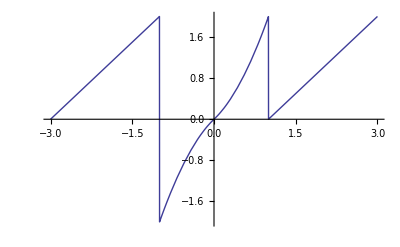

```mathematica
graphone=Plot[f[x],{x,-3,3}]
```

```mathematica
(*Manipulate[  consider manipulating k to find a reasonable value*)
```

```mathematica
graphtwo=Plot[fourier[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

-Graphics-

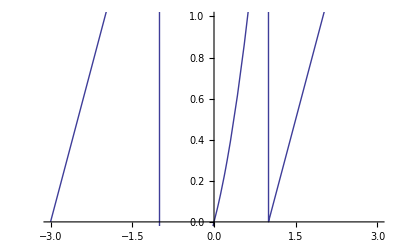

```mathematica
bothtwo=Show[graphtwo,graphone]
```

```mathematica
graphthree=Plot[fourier[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

-Graphics-

```mathematica
boththree=Show[graphthree,graphone]
```

-Graphics-

```mathematica
graphsix=Plot[fourier[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 14 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 15 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 16 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 17 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 18 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 19 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 20 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 12 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 13 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 14 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 15 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 16 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 17 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 18 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 19 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 20 of {{0.`, 0.6366197723675814` f}, {0.`, -0.3183098861837907` f}, {0.`, 0.2122065907891938` f}, {0.`, -0.15915494309189535` f}, {0.`, « 20 » f}, {0.`, « 1 »}, {0.`, 0.09094568176679733` f}, {0.`, -0.07957747154594767` f}, {0.`, 0.07073553026306459` f}, {0.`, -0.06366197723675814` f}} does not exist.

Part::partw: Part 11 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 12 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

Part::partw: Part 13 of {{0, 2 f/π}, {0, -f/π}, {0, 2 f/3 π}, {0, -f/2 π}, {0, 2 f/5 π}, {0, -f/3 π}, {0, 2 f/7 π}, {0, -f/4 π}, {0, 2 f/9 π}, {0, -f/5 π}} does not exist.

```mathematica
bothsix=Show[graphsix,graphone]
```

Show::gcomb: Could not combine the graphics objects in Show[graphsix, GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[138]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-3, 3], List[-1.9972929720748862`, 1.9999998775510206`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]].

Show[graphsix,-Graphics-]

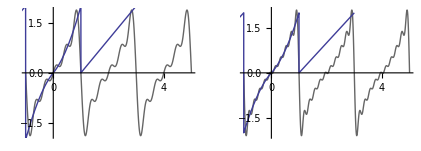

```mathematica
Show[GraphicsRow[{bothtwo,boththree,bothsix}]]
```

```mathematica
(*Begin of Problem #4*)
```